```mathematica
k1Error2D=Table[Timing[Sqrt[.042^2 Sum[(reconstructk[1,#,{x,y},{n,n}]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@fullCoefficientsk[1,Sin[Pi #⟦1⟧+#⟦2⟧]&,{n,n}]],{n,1,4}]
```

{{0.302592,0.328752},{0.872219,0.173534},{2.44406,0.0939316},{8.0308,0.0444521}}

```mathematica
k2Error2D=Table[Timing[Sqrt[.042^2 Sum[(reconstructk[2,#,{x,y},{n,n}]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@fullCoefficientsk[2,Sin[Pi #⟦1⟧+#⟦2⟧]&,{n,n}]],{n,1,4}]
```

{{1.51376,0.0657847},{5.10616,0.0178579},{16.9582,0.00528572},{60.6625,0.00119287}}

```mathematica
k3Error2D=Table[Timing[Sqrt[.042^2 Sum[(reconstructk[3,#,{x,y},{n,n}]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@fullCoefficientsk[3,Sin[Pi #⟦1⟧+#⟦2⟧]&,{n,n}]],{n,1,3}]
```

{{4.65329,0.00897283},{17.6187,0.00125538},{58.2391,0.000180915}}

```mathematica
k4Error2D=Table[Timing[Sqrt[.031^2 Sum[(reconstructk[4,#,{x,y},{n,n}]-Sin[Pi x+y])^2,{x,0,1,.031},{y,0,1,.031}]]&@fullCoefficientsk[4,Sin[Pi #⟦1⟧+#⟦2⟧]&,{n,n}]],{n,1,3}]
```

```mathematica
sparsek1Error2D=Table[Timing[Sqrt[.021^2 Sum[(sparseReconstructk[1,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.021},{y,0,1,.021}]]&@sparseCoefficientsk[1,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2]],{n,1,4}]
```

{{0.837279,0.356328},{1.61718,0.197855},{2.66111,0.107699},{4.44653,0.0584674}}

```mathematica
sparsek2Error2D=Table[Timing[Sqrt[.042^2 Sum[(sparseReconstructk[2,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@sparseCoefficientsk[2,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2]],{n,1,4}]

sparsek3Error2D=Table[Timing[Sqrt[.042^2 Sum[(sparseReconstructk[3,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@sparseCoefficientsk[3,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2]],{n,1,4}]

sparsek4Error2D=Table[Timing[Sqrt[.042^2 Sum[(sparseReconstructk[4,#,{x,y},n]-Sin[Pi x+y])^2,{x,0,1,.042},{y,0,1,.042}]]&@sparseCoefficientsk[4,Sin[Pi #⟦1⟧+#⟦2⟧]&,n,2]],{n,1,4}]
```

{{0.224481,0.359123},{0.449861,0.201665},{0.886656,0.114207},{1.68566,0.0613282}}

{{1.01228,0.0666076},{2.64378,0.0182149},{6.01789,0.00540757},{12.6867,0.00124363}}

{{2.71548,0.00897328},{7.9628,0.00125529},{19.4037,0.000180842},{43.5602,0.0000185444}}

{{7.02033,0.000970717},{24.3021,0.0000723841},{61.3493,4.84515×10^-6},{137.362,0.0000205265}}

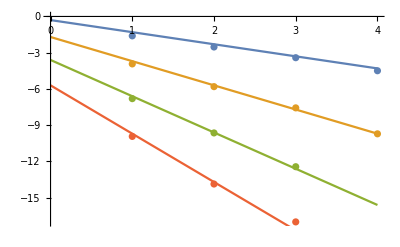

```mathematica
Show[ListPlot[{k1Error2D[[;;,2]],k2Error2D[[;;,2]],k3Error2D[[;;,2]],k4Error2D[[;;,2]]}//Log2],Plot[{-x-.3,-2x-1.7,-3x-3.6,-4x-5.7},{x,0,4}]]
```

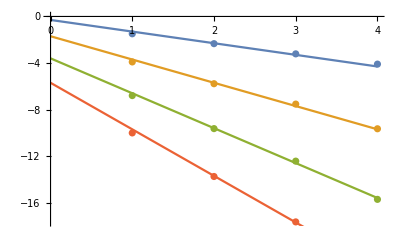

```mathematica
Show[ListPlot[{sparsek1Error2D[[;;,2]],sparsek2Error2D[[;;,2]],sparsek3Error2D[[;;,2]],sparsek4Error2D[[;;3,2]]}//Log2],Plot[{-x-.3,-2x-1.7,-3x-3.6,-4x-5.7},{x,0,4}]]
```

```mathematica
sparseLengthsk1=Table[Length[sparseIterate[1,n,2]],{n,1,4}];
sparseLengthsk2=Table[Length[sparseIterate[2,n,2]],{n,1,4}];
sparseLengthsk3=Table[Length[sparseIterate[3,n,2]],{n,1,4}];
sparseLengthsk4=Table[Length[sparseIterate[4,n,2]],{n,1,4}];
```

```mathematica
fullLengthsk1=Table[Length[hierIterate[1,{n,n}]],{n,1,4}];
fullLengthsk2=Table[Length[hierIterate[2,{n,n}]],{n,1,4}];
fullLengthsk3=Table[Length[hierIterate[3,{n,n}]],{n,1,4}];
fullLengthsk4=Table[Length[hierIterate[4,{n,n}]],{n,1,4}];
```

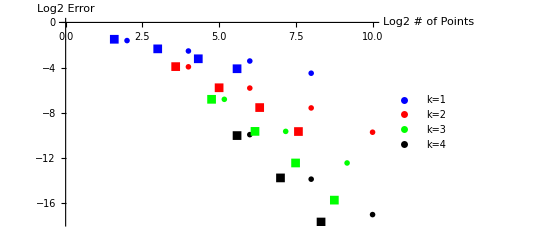

```mathematica
ListPlot[{Table[{fullLengthsk1⟦n⟧,k1Error2D⟦n,2⟧},{n,1,4}],Table[{fullLengthsk2⟦n⟧,k2Error2D⟦n,2⟧},{n,1,4}],Table[{fullLengthsk3⟦n⟧,k3Error2D⟦n,2⟧},{n,1,3}],
Table[{fullLengthsk4[[n]],k4Error2D[[n,2]]},{n,1,3}],Table[{sparseLengthsk1⟦n⟧,sparsek1Error2D⟦n,2⟧},{n,1,4}],Table[{sparseLengthsk2⟦n⟧,sparsek2Error2D⟦n,2⟧},{n,1,4}],
Table[{sparseLengthsk3⟦n⟧,sparsek3Error2D⟦n,2⟧},{n,1,4}],Table[{sparseLengthsk4⟦n⟧,sparsek4Error2D⟦n,2⟧},{n,1,3}]}//Log2,PlotStyle->{Blue,Red,Green,Black,Blue,Red,Green,Black},PlotMarkers->{●,●,●,●,■,■,■,■},PlotLegends->{"k=1","k=2","k=3","k=4"},AxesLabel->{"Log2 # of Points", "Log2 Error"}]
```

```mathematica
●
```

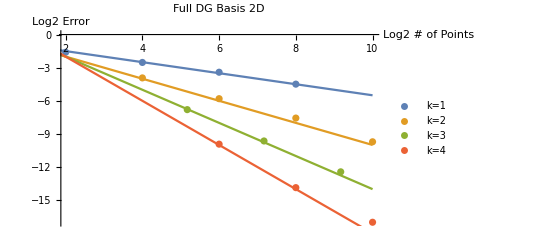

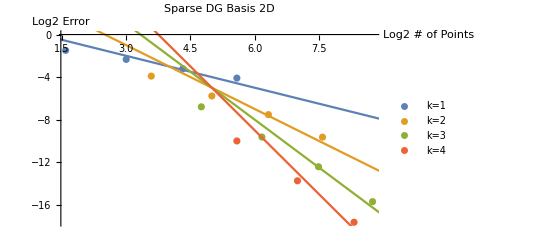

```mathematica
Show[ListPlot[{Table[{fullLengthsk1⟦n⟧,k1Error2D⟦n,2⟧},{n,1,4}],Table[{fullLengthsk2⟦n⟧,k2Error2D⟦n,2⟧},{n,1,4}],Table[{fullLengthsk3⟦n⟧,k3Error2D⟦n,2⟧},{n,1,3}],
Table[{fullLengthsk4[[n]],k4Error2D[[n,2]]},{n,1,3}]}//Log2,PlotLegends->{"k=1","k=2","k=3","k=4"},AxesLabel->{"Log2 # of Points", "Log2 Error"},PlotLabel->Style["Full DG Basis 2D",Black,Larger,Bold]],Plot[{-1/2 x-.5,-1 x,-3/2 x+1, -2x+2},{x,0,10}]]


Show[ListPlot[{Table[{sparseLengthsk1⟦n⟧,sparsek1Error2D⟦n,2⟧},{n,1,4}],Table[{sparseLengthsk2⟦n⟧,sparsek2Error2D⟦n,2⟧},{n,1,4}],
Table[{sparseLengthsk3⟦n⟧,sparsek3Error2D⟦n,2⟧},{n,1,4}],Table[{sparseLengthsk4⟦n⟧,sparsek4Error2D⟦n,2⟧},{n,1,3}]}//Log2,PlotLegends->{"k=1","k=2","k=3","k=4"},AxesLabel->{"Log2 # of Points", "Log2 Error"},PlotLabel->Style["Sparse DG Basis 2D",Black,Larger,Bold]],Plot[{-x+1,-2x+5,-3x+10,-4x+15},{x,0,10}]]
```

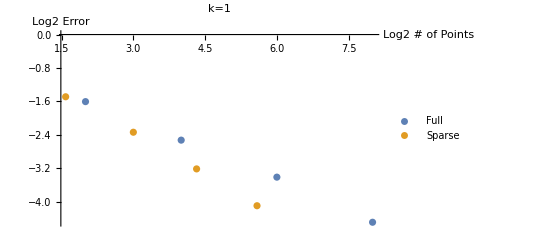

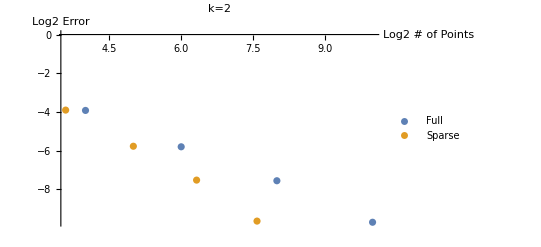

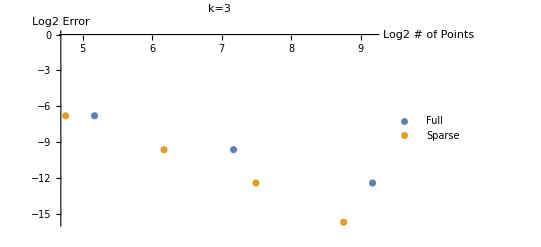

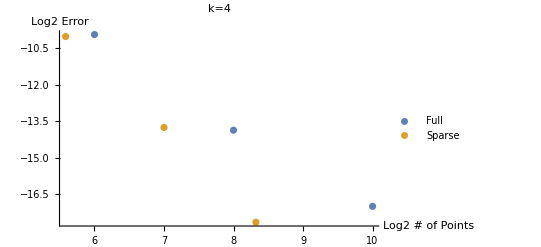

```mathematica
ListPlot[{Table[{fullLengthsk1⟦n⟧,k1Error2D⟦n,2⟧},{n,1,4}],Table[{sparseLengthsk1⟦n⟧,sparsek1Error2D⟦n,2⟧},{n,1,4}]}//Log2,AxesLabel->{"Log2 # of Points", "Log2 Error"},PlotLegends->{"Full","Sparse"},PlotLabel->Style["k=1",Black,Bold]]
ListPlot[{Table[{fullLengthsk2⟦n⟧,k2Error2D⟦n,2⟧},{n,1,4}],Table[{sparseLengthsk2⟦n⟧,sparsek2Error2D⟦n,2⟧},{n,1,4}]}//Log2,AxesLabel->{"Log2 # of Points", "Log2 Error"},PlotLegends->{"Full","Sparse"},PlotLabel->Style["k=2",Black,Bold]]
ListPlot[{Table[{fullLengthsk3⟦n⟧,k3Error2D⟦n,2⟧},{n,1,3}],Table[{sparseLengthsk3⟦n⟧,sparsek3Error2D⟦n,2⟧},{n,1,4}]}//Log2,AxesLabel->{"Log2 # of Points", "Log2 Error"},PlotLegends->{"Full","Sparse"},PlotLabel->Style["k=3",Black,Bold]]

ListPlot[{Table[{fullLengthsk4⟦n⟧,k4Error2D⟦n,2⟧},{n,1,3}],Table[{sparseLengthsk4⟦n⟧,sparsek4Error2D⟦n,2⟧},{n,1,3}]}//Log2,AxesLabel->{"Log2 # of Points", "Log2 Error"},PlotLegends->{"Full","Sparse"},PlotLabel->Style["k=4",Black,Bold],PlotRange->Automatic]
```